# Лабораторная работа 8

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр . Ковалевская В . С .
    20 октября 2021

## Задание 1

Осуществите параллельный перенос.

```mathematica
Fig1=Graphics3D[{AbsoluteThickness[3],Line[{{0,0,0},{1,0,0}}]}, Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
ab={{0,0,0},{1,0,0}};
v={0,1,0};
(#+v)&/@ab
```

{{0,1,0},{1,1,0}}

```mathematica
Fig2=Graphics3D[{{AbsoluteThickness[3],Hue[0],Line[ab]},{AbsoluteThickness[3],Hue[.5],Line[(#+v)&/@ab](*отобразили исходный отрезок и его образ*)}},Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
Fig1//FullForm
```

Graphics3D[List[AbsoluteThickness[3],Line[List[List[0,0,0],List[1,0,0]]]],Rule[Axes,True],Rule[AxesLabel,List["X","Y","Z"]]]

```mathematica
Fig1/.Line[P_]:>{Line[P],Hue[0.3],Line[#+{0,1,0}&/@P]}//FullForm
```

Graphics3D[List[AbsoluteThickness[3],List[Line[List[List[0,0,0],List[1,0,0]]],Hue[0.3],Line[List[List[0,1,0],List[1,1,0]]]]],Rule[Axes,True],Rule[AxesLabel,List["X","Y","Z"]]]

```mathematica
Fig2=Show[Fig1/.Line[P_]:>{Line[P],Hue[.5],Line[#+{0,1,0}&/@P]},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
ab={{0,0,0},{1,0,0}};
v={0,1,0};
{#,#+v}&/@ab
```

{{{0,0,0},{0,1,0}},{{1,0,0},{1,1,0}}}

```mathematica
Fig2=Show[Fig1/.Line[P_]:>{Line[P],Line[#+v&/@P],Hue[.5],Line[{#,#+v}]&/@P},Boxed->False,Axes->False](*результат клонироапния отрезка*)
```

-Graphics3D-

```mathematica
Fig3=Show[Fig2/.Line[P_]:>{Line[P],Line[#+{0,0,1}&/@P],Hue[1/3],Line[{#,#+{0,0,1}}]&/@P},Boxed->False,Axes->False](*результат двукратного выполнения операции клонирования*)
```

-Graphics3D-

```mathematica
Line[P_]:>{Line[P],Line[#+Vector]&/@P,Line[{#,#+Vector}]&/@P}
```

Line[P_]:>{Line[P],(Line[#1+Vector]&)/@P,(Line[{#1,#1+Vector}]&)/@P}

```mathematica
Shift[Fig_,Vector_,Color_]:=Fig/.Line[P_]:>{Line[P],Line[#+Vector&/@P],Color,Line[{#,#+Vector}]&/@P}
```

```mathematica
Show[Fig4=Shift[Fig3,{1.5,1,1},Hue[12]]]
```

-Graphics3D-

```mathematica
Show[Fig5=Shift[Fig4,{-1.5,1,1},Hue[1/6]]]
```

-Graphics3D-

## Задание 2

Напишите функцию fracLine[{A : {_, _}, B : {_, _}}], генерирующую из произвольного отрезка AB указанный фрактальный
фрагмент, согласно варианту .

```mathematica
ClearAll[fracLine];
fracLine[{A:{_,_},B:{_,_}}]:=Partition[{A,A+(B-A)/(100/47),A+(B-A)/2+0.47 {{0,-1},{1,0}}.(B-A),A+(B-A)/(100/53),B},2,1]
```

```mathematica
Partition[{a,b,c,s,d,e},2,1]
```

{{a,b},{b,c},{c,s},{s,d},{d,e}}

```mathematica
fracLine[{{0,0},{1,0}}]//Flatten[#,1]&
```

{{0,0},{47/100,0},{47/100,0},{0.5,0.47},{0.5,0.47},{53/100,0},{53/100,0},{1,0}}

```mathematica
fracLine[coord_]:=coord/.{A:{_,_},B:{_,_}}:>Partition[{A,A+0.47 (B-A),A+(B-A)/2+0.47*{{0,-1},{1,0}}.(B-A),A+0.53 (B-A),B},2,1]
```

```mathematica
fracLine[{{0,0},{1,0}}]
```

{{{0,0},{47/100,0}},{{47/100,0},{0.5,0.47}},{{0.5,0.47},{53/100,0}},{{53/100,0},{1,0}}}

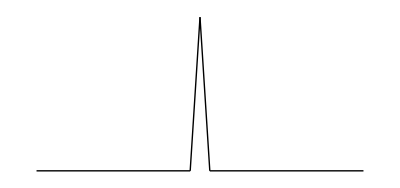

```mathematica
Graphics[{Line[fracLine[{{0,0},{1,0}}]]}]
```

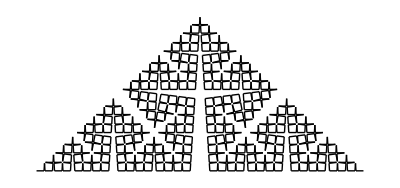

```mathematica
Graphics[Line[#]&/@fracLine[#]&/@fracLine[#]&/@fracLine[#]&/@fracLine[#]&/@fracLine[{{0,0},{1,0}}]]
```

```mathematica
mycoord={{{0,0},{1,0}},{{1,0},{1,1}},{{1,1},{0,1}},{{0,1},{0,0}}}
```

{{{0,0},{1,0}},{{1,0},{1,1}},{{1,1},{0,1}},{{0,1},{0,0}}}

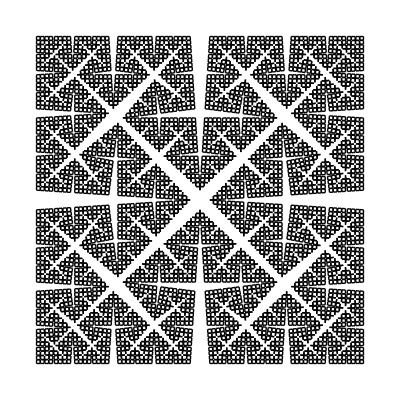

```mathematica
Graphics[Line[#]&/@fracLine[#]&/@fracLine[#]&/@fracLine[#]&/@fracLine[#]&/@fracLine[#]&/@fracLine[mycoord]]
```

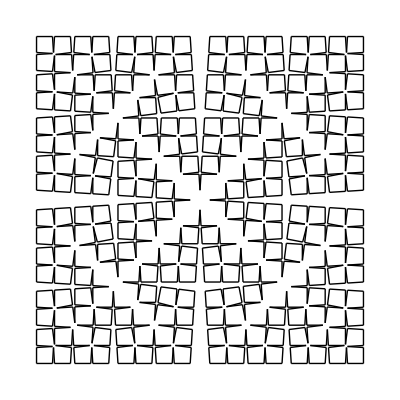

```mathematica
Graphics[Line[#]&/@fracLine[#]&/@fracLine[#]&/@fracLine[#]&/@fracLine[mycoord]]
```

```mathematica
fracLine[coord_]:=coord/.{A:{_,_},B:{_,_}}:>Partition[{A,A+0.47 (B-A),A+(B-A)/2+0.47*{{0,-1},{1,0}}.(B-A),A+0.53 (B-A),B},2,1]//Flatten[#,1]&
```

```mathematica
fracLine[{{0,0},{1,0}}]
```

{{{0,0},{47/100,0}},{{47/100,0},{0.5,0.47}},{{0.5,0.47},{53/100,0}},{{53/100,0},{1,0}}}

```mathematica
{{{0,0},{47/100,0}},{{47/100,0},{0.5,0.47}},{{0.5,0.47},{53/100,0}},{{53/100,0},{1,0}}}
```

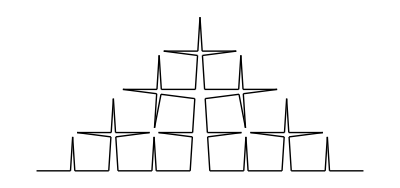

```mathematica
Graphics[Line[Nest[fracLine,{{0,0},{1,0}},3]]]
```

```mathematica
ClearAll[fracShow];
fracShow[{A:{_,_},B:{_,_}},n_Integer?Positive]:=Graphics[{Line[Nest[fracLine,{A,B},n]]}]
```

```mathematica
Graphics[{Line[Nest[fracLine,mycoord,6]]}]
```

-Graphics-